```mathematica
(*TOMA DE DATOS*)
```

```mathematica
(*CALENTAMIENTO*)
```

```mathematica
VCal={0.4,0.47,0.54,0.62,0.70,0.79,0.89,1.00,1.11,1.24,1.36,1.51,1.66,1.95,2.11,2.30,2.50,2.71,2.93,3.14};(*mV*)
```

```mathematica
PCal=VCal/0.16;(*mW*)
```

```mathematica
TCal={100,110,120,130,140,150,160,170,180,190,200,210,220,240,250,260,270,280,290,300}+273.15;(*K*)
```

```mathematica
dataCal=Transpose[{(TCal^4)/10^10,PCal}];
```

```mathematica
(*ENFRIAMIENTO*)
```

```mathematica
VEnf={2.93,2.75,2.58,2.41,2.26,2.12,1.97,1.83,1.69,1.54,1.41,1.28,1.15,1.04,0.91};(*mV*)
```

```mathematica
PEnf=VEnf/0.16;(*mW*)
```

```mathematica
TEnf={290,280,270,260,250,240,230,220,210,200,190,180,170,160,150}+273.15;(*K*)
```

```mathematica
dataEnf=Transpose[{(TEnf^4)/10^10,PEnf}];
```

```mathematica
(*ANÁLISIS DE DATOS*)
```

```mathematica
(*CALENTAMIENTO*)
```

```mathematica
fitCal=NonlinearModelFit[dataCal,A+B*x,{A,B},x]
```

FittedModel[…]

```mathematica
fitCal[{"BestFit","ParameterTable"}]
```

{-1.23569+1.93876 x, | Estimate | Standard Error | t-Statistic | P-Value
A | -1.23569 | 0.0293242 | -42.1388 | 1.92304×10^-19
B | 1.93876 | 0.00480036 | 403.878 | 4.4958×10^-37}

```mathematica
plotfitCal=Plot[fitCal[x],{x,0,30},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Red,White}],Thick},PlotRange->{{1.7,11},{2.2,20}},Frame->True,FrameLabel->{Style["T⁴ / 10.b9⁰ K⁴",Bold,16],Style["P / mW",16,Bold]}];
```

```mathematica
plotdataCal=ListPlot[dataCal,PlotStyle->{Black,Thickness[0.003]}];
```

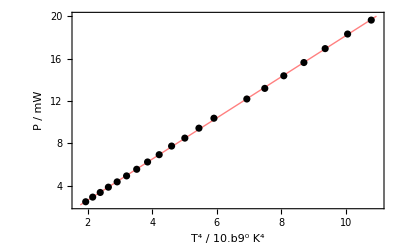

```mathematica
Show[plotfitCal,plotdataCal]
```

```mathematica
(*ENFRIAMIENTO*)
```

```mathematica
fitEnf=NonlinearModelFit[dataEnf,A+B*x,{A,B},x]
```

FittedModel[…]

```mathematica
fitEnf[{"BestFit","ParameterTable"}]
```

{0.318127+1.82536 x, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.318127 | 0.212077 | 1.50005 | 0.15749
B | 1.82536 | 0.0324325 | 56.2818 | 6.48166×10^-17}

```mathematica
plotfitEnf=Plot[fitEnf[x],{x,0,40},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{3,10.2},{6,18.5}},Frame->True,FrameLabel->{Style["T⁴ / 10.b9⁰ K⁴",Bold,16],Style["P / mW",16,Bold]}];
```

```mathematica
plotdataEnf=ListPlot[dataEnf,PlotStyle->{Black,Thickness[0.003]}];
```

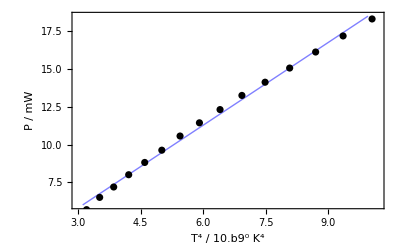

```mathematica
Show[plotfitEnf,plotdataEnf]
```

```mathematica
(*ln(P+P0)*)
```

```mathematica
(*CALENTAMIENTO*)
```

```mathematica
dataCal2=Transpose[{Log[TCal],Log[PCal+1.2356884207856167]}];
```

```mathematica
fitCal2=NonlinearModelFit[dataCal2,A+B*x,{A,B},x]
```

FittedModel[…]

```mathematica
fitCal2[{"BestFit","ParameterTable"}]
```

{-22.4365+4.01174 x, | Estimate | Standard Error | t-Statistic | P-Value
A | -22.4365 | 0.0558747 | -401.55 | 4.98885×10^-37
B | 4.01174 | 0.00908676 | 441.492 | 9.05246×10^-38}

```mathematica
plotfitCal2=Plot[fitCal2[x],{x,0,30},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Red,White}],Thick},PlotRange->{{5.9,6.36},{1.3,3.1}},Frame->True,FrameLabel->{Style["Log[T / K]",Bold,16],Style["Log[P+Pₒ / mW]",16,Bold]}];
```

```mathematica
plotdataCal2=ListPlot[dataCal2,PlotStyle->{Black,Thickness[0.003]}];
```

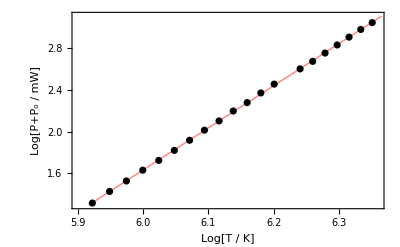

```mathematica
Show[plotfitCal2,plotdataCal2]
```

```mathematica
(*ENFRIAMIENTO*)
```

```mathematica
dataEnf2=Transpose[{Log[TEnf],Log[PEnf-0.31812694686808046]}];
```

```mathematica
fitEnf2=NonlinearModelFit[dataEnf2,A+B*x,{A,B},x]
```

FittedModel[…]

```mathematica
fitEnf2[{"BestFit","ParameterTable"}]
```

{-23.2822+4.13798 x, | Estimate | Standard Error | t-Statistic | P-Value
A | -23.2822 | 0.530756 | -43.8662 | 1.62866×10^-15
B | 4.13798 | 0.0856392 | 48.3188 | 4.66785×10^-16}

```mathematica
plotfitEnf2=Plot[fitEnf2[x],{x,0,30},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{6.07,6.34},{1.9,3.0}},Frame->True,FrameLabel->{Style["Log[T / K]",Bold,16],Style["Log[P+Pₒ / mW]",16,Bold]}];
```

```mathematica
plotdataEnf2=ListPlot[dataEnf2,PlotStyle->{Black,Thickness[0.003]}];
```

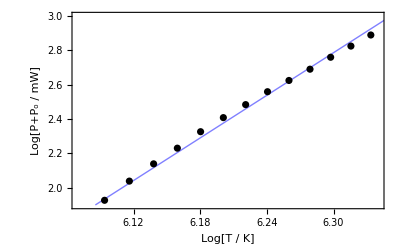

```mathematica
Show[plotfitEnf2,plotdataEnf2]
```

```mathematica
(*OTROS CÁLCULOS*)
```

```mathematica
Sprime=Pi*(12.5)^2;(*mm^2*)
```

```mathematica
ra=10;(*mm*)
```

```mathematica
d=120;(*mm*)
```

```mathematica
f=(Sprime*ra^2/(d^2))*10^(-6)(*m^2*)
```

3.40885×10^-6

```mathematica
Errf=(2*f*1.4/d)(*m^2*)
```

7.95397×10^-8

```mathematica
SigmaTab=5.670374*10^-8;
```

```mathematica
(*SIGMA CALENTAMIENTO*)
```

```mathematica
SigmaCal=1.938762432097837*10^-13/f (*W/m2 K4*)
```

5.68744×10^-8

```mathematica
ErrSigmaCal=Sqrt[(0.004800362231865056*10^-13/f)^2+(1.938762432097837*10^-13*Errf/f^2)^2]
```

1.40821×10^-10

```mathematica
DifRelCal=(Abs[SigmaTab-SigmaCal]/SigmaTab)*100
```

0.301051

```mathematica
(*SIGMA ENFRIAMIENTO*)
```

```mathematica
SigmaEnf=1.8253596131651195*10^-13/f
```

5.35477×10^-8

```mathematica
ErrSigmaEnf=Sqrt[(0.03243252895948919*10^-13/f)^2+(1.8253596131651195*10^-13*Errf/f^2)^2]
```

9.51422×10^-10

```mathematica
DifRelEnf=(Abs[SigmaTab-SigmaEnf]/SigmaTab)*100
```

5.5658

```mathematica
(*h Planck con CALENTAMIENTO*)
```

```mathematica
h=((2*(Pi^5)*((1.380658.08*10^(-23))^4))/(15*(299792458)^2*SigmaCal))^(1/3)
```

6.61949×10^-34 ((.08)^4)^(1/3)

```mathematica
htab=6.62607015*10^(-34);
```

```mathematica
DifRelh=(Abs[htab-6.6194918730196354*^-34]/htab)*100
```

0.0992787

```mathematica
(*T0 con calentamiento*)
T0Cal=(1.2356884207856167*10^(-3)/(f*SigmaCal))^(1/4)-273.15
```

9.40051